```mathematica
Needs["NDSolve`FEM`"]
region=Line[{{0},{1}}];
includePoints={{1/3},{2/3}};
mesh=ToElementMesh[region,"IncludePoints"->includePoints,"MaxCellMeasure"->0.0008]
```

ElementMesh[{{0.,1.}},{LineElement[<1248>]}]

```mathematica
vars={c[t,x],t,{x}};
pars=<|"DiffusionCoefficient"->1,"MassConvectionVelocity"->{100}|>;
```

```mathematica
RegularizedDeltaPoint[g_,X_List,Xs_List]:=Piecewise[{{Times@@Thread[1/(4 g) (1+Cos[π/(2 g) (X-Xs)])],And@@Thread[RealAbs[X-Xs]≤2 g]},{0,True}}]
```

```mathematica
Subscript[h,mesh]=Sqrt[Min[mesh["MeshElementMeasure"]]];
Subscript[gamma,reg]=Subscript[h,mesh]/2;
```

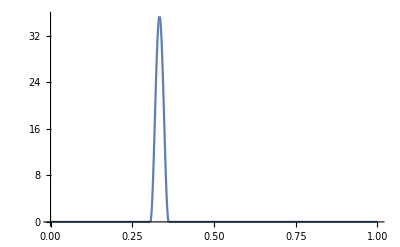

```mathematica
temp=RegularizedDeltaPoint[Subscript[gamma,reg],{x},includePoints[[1]]];
Plot[temp,{x,0,1}]
```

```mathematica
Qp=10;
pars["MassSource"]=RegularizedDeltaPoint[Subscript[gamma,reg],{x},includePoints[[1]]]*Qp+RegularizedDeltaPoint[Subscript[gamma,reg],{x},includePoints[[2]]]*If[t>1/2*10^-3,5*Qp,0];
```

```mathematica
pde={MassTransportPDEComponent[vars,pars]==0,c[0,x]==0};
tEnd=10^-3;
cfun=NDSolveValue[pde,c,{t,0,tEnd},{x}∈mesh];
```

NDSolveValue::derivs: No derivatives of dependent variables were found in the equations. NDSolveValue is designed to solve differential or differential algebraic equations. Use NSolve or FindRoot to numerically solve algebraic equations.

```mathematica
Manipulate[Plot[cfun[t,x],{x}∈region,PlotRange->{{0,1},{0,1/2}}],{t,0,tEnd}]
```

NDSolveValue::dsvar: 0. cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.